```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
C0=1;C1=0.6;C2=0.35;C3=0.2;τ2=0.4;τ1=τ2-δ;τ3=1-δ;
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=570;ω1=0.5;ω2=3;
t1=20;t2=40;t3=60;t4=80;t5=100;
t6=120;t7=135;t8=150;t9=165;t10=175;t11=210;
t12=211;t13=250;t14=251;t15=280;
t16=281;t17=300;t18=301;t19=320;t20=350;
t21=t20+8*2Pi/ω1;
t22=470;t23=t22+30*2Pi/ω2;
t24=550;t25=560;t26=570;
Ct[t_]=Which[
t<t1,C0,
t<t2,C0+(t-t1)/(t2-t1)(C3-C0), 
t<t3,C3,
t<t4,C3+(t-t3)/(t4-t3)(C0-C3),
t<t5,C0,
t<t6,0.7,
t<t7,0.4,
t<t8,0.55,
t<t9,0.65,
t<t10,0.8,
t<t11,C0,
t<t12,C0+(t-t11)/(t12-t11)(C2-C0), 
t<t13,C2,
t<t14,C2+(t-t13)/(t14-t13)(C0-C2),
t<t15,C0,
t<t16,C0+(t-t15)/(t16-t15)(C1-C0), 
t<t17,C1,
t<t18,C1+(t-t17)/(t18-t17)(C0-C1),
t<t19,C0,
t<t20,C0+(t-t19)/(t20-t19) (C1-C0),
t<t21,C1 + 0.3Sin[ω1(t-t20)],
t<t22,C1,
t<t23,C1 + 0.3Sin[ω2(t-t22)],
t<t24,C1,
t<t25,C1+(t-t24)/(t25-t24)(C0-C1),
t<t26,C0,
True,1
];

(*Compute equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
```

```mathematica
(*Simulation*)
{U1,W1}=NDSolveValue[{u'[t] ==u[t]/Ct[t]-u[t]^3/(3Ct[t]^3)-w[t],w'[t]==ep(u[t]/Ct[t]-γ w[t] + β),u[0]==Ct[0]v0,w[0]==w0},{u,w},{t,0,maxtime},MaxStepSize->0.006];
```

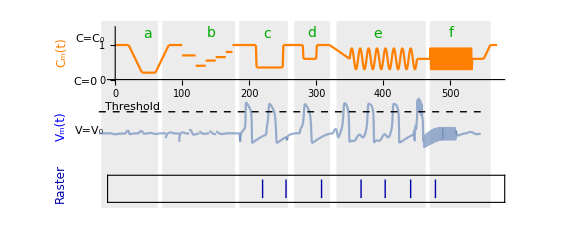

Fig1.svg

```mathematica
(*Generate Figure*)
capacitance=Plot[{Ct[t]},{t,0,maxtime},PlotPoints->10000,MaxRecursion->3,PlotStyle->Orange, AspectRatio->1/8,PlotRange->{{0,maxtime},{0,1.5}},ImageSize->Large,ImagePadding->{{20,20},{4,5}},Frame->False,Axes->{True,False},FrameLabel->{"","Capacitance"},TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic},Ticks->{None,{0,0.5,1}}];
tags=ListPlot[{
Labeled[{35,1.1},Style["a",Darker[Green],FontSize->14],Background->None]
,Labeled[{130,1.1},Style["b",Darker[Green],FontSize->14],Background->None]
,Labeled[{240,1.1},Style["c",Darker[Green],FontSize->14],Background->None]
,Labeled[{307,1.1},Style["d",Darker[Green],FontSize->14],Background->None]
,Labeled[{378,1.1},Style["e",Darker[Green],FontSize->14],Background->None]
,Labeled[{490,1.1},Style["f",Darker[Green],FontSize->14],Background->None]
},PlotStyle->{Opacity[0]}];
voltage=Plot[U1[t]/Ct[t],{t,0,maxtime},PlotRange->{{0,maxtime},{-2.5,2.5}},PlotPoints->10000, AspectRatio->1/8,ImageSize->Large,ImagePadding->{{50,20},{0,0}},Frame->False,Axes->{False,False},FrameLabel->{None,"Voltage"},PlotStyle->{Opacity[0.6]},FrameTicks->{Automatic,{-2,0,2}},Epilog->Style[Text["Threshold",{50,1.45}],FontSize->11]];
thresholdLine=Graphics[{Dashed, Line[{{0,1},{maxtime,1}}]}];

peaks = FindPeaks[Table[U1[t]/Ct[t],{t,1,maxtime,1}],2,0,1];
rasterLines=Table[ Graphics[{Thick,Darker[Blue], Line[{{xk[[1]],-1},{xk[[1]],1}}]}],{xk,peaks}];
rasterCanvas=ListPlot[Table[ {xk[[1]],0},{xk,peaks}], AspectRatio->1/16,ImageSize->Large,Axes->{False,False},Frame->True,FrameTicks->False,PlotRange->{{0,maxtime},{-1.4,1.4}},ImagePadding->{{50,20},{2,0}},PlotStyle->PointSize[0]];

g1=GraphicsGrid[{ {Show[capacitance,tags]},{Show[voltage,thresholdLine]},{Show[rasterCanvas,rasterLines]}}];
bands={Graphics[{Gray,Opacity[0.15],Rectangle[{70,-215},{140,0}]}],
Graphics[{Gray,Opacity[0.15],Rectangle[{145,-215},{235,0}]}],
Graphics[{Gray,Opacity[0.15],Rectangle[{240,-215},{300,0}]}],
Graphics[{Gray,Opacity[0.15],Rectangle[{308,-215},{352,0}]}],
Graphics[{Gray,Opacity[0.15],Rectangle[{360,-215},{470,0}]}],
Graphics[{Gray,Opacity[0.15],Rectangle[{475,-215},{550,0}]}]
};
tagsFinal=ListPlot[{
Labeled[{35,-80},Style["C=0"],Background->None],
Labeled[{35,-35},Style["C=C_0"],Background->None],
Labeled[{35,-140},Style["V=V_0"],Background->None]
},PlotStyle->{Opacity[0]}];
labels=ListPlot[{
Labeled[{10,-60},Rotate[Style["C_m(t)",FontSize->12,Orange],Pi/2]],
Labeled[{10,-145},Rotate[Style["V_m(t)",FontSize->12,Blue],Pi/2]],
Labeled[{10,-215},Rotate[Style["Raster",FontSize->12,Darker[Blue]],Pi/2]]
},PlotStyle->{Opacity[0]}];
g2=Show[bands,g1,tagsFinal,labels,ImageSize->Large]
Export["Fig1.svg",g2]
```